```mathematica
(* notebook to manipulate the stringbit numerical results. *)
(* depends on perturb.nb *)

ClearAll[ResultFolder,LoadEnergyData,LoadTotalEnergy,LoadEvsS];
ResultFolder = NotebookDirectory[]<>"../results/";
Format[energy,StandardForm]="E";

Options[LoadTotalEnergy]={Folder->ResultFolder,NormalizeFactorM->0};
LoadTotalEnergy[s_,xi_,opts:OptionsPattern[]]:=Module[{file,data,normpower},
file = "Es="<> ToString[s] <> "xi="<>ToString[xi];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];

normpower = OptionValue[NormalizeFactorM];
Do[data[[i,2]]=N[data[[i,2]]/data[[i,1]]^normpower], {i,1,Length[data]}];
Return[data];
];

(*DataSet: 0 for all data point, 1 for odd only, 2 for even only *)
Options[LoadEvsS]={LogData->False,DataSet->0,Folder->ResultFolder};
LoadEvsS[M_,xi_,opts:OptionsPattern[]]:=Module[{file,data,i,len,ret={}},
file = "Exi="<> ToString[xi] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];
If[OptionValue[LogData],
For[i=1,i≤ Length[data],i++,
data[[i,2]]=Log10[Abs[data[[i,2]]]];
];
];

If[OptionValue[DataSet]==0, Return[data]];

len = Length[data];
For[i=1,i≤Length[data],i++,
If[Mod[data[[i,1]],2]== Mod[OptionValue[DataSet],2],
AppendTo[ret, data[[i]]];
];
];
Return[ret];

(*If[OptionValue[DataSet] == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];*)
];


(*DataSet: 0 for all data point, 1 for odd only, 2 for even only, 3 for data[L] + data[M-L] *)
Options[LoadEnergyData]={DataSet->0,NormalizeFactorM->0,Folder->ResultFolder};
LoadEnergyData[s_,xi_,M_,opts:OptionsPattern[]]:=Module[{file,data,dataType, ret, len,normpower},
file = "s="<>ToString[s]<>"-M="<>ToString[M];
If[xi≠0, file = file <> "-xi="<>ToString[xi]];
data=Import[OptionValue[Folder]<>file<>".txt","Table"];

normpower = OptionValue[NormalizeFactorM];
data=data[[2;;Length[data],{2,3}]];
Do[data[[i,1]]=N[data[[i,1]]/M];data[[i,2]]=N[data[[i,2]]/(M^normpower)], {i,1,Length[data]}];

dataType = OptionValue[DataSet];
If[dataType == 0,  Return[data]];
len = Length[data];

If[dataType == 3,
Return[Table[{data[[2i-1,1]], data[[2i-1,2]]+data[[len-2i+2,2]]},{i,1,Round[len/2]}]]
];

If[dataType == 1, 
Return[Table[data[[2*i-1]],{i,1,Floor[(len+1)/2]}]]
];

If[dataType == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];
];

AxesFontSize=14;
LabelFontSize = 16;

ClearAll[PlotEnergyCorrection];
Options[PlotEnergyCorrection]=Join[{LegendPos->{0.15,70}},Options[ListPlot],Options[LoadEnergyData]];
PlotEnergyCorrection[s_,xi_,Mlist_,showLegends_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,toPlot,m,options},
For[i=1,i≤ Length[Mlist],i++,
m = Mlist[[i]];
toPlot=LoadEnergyData[s,xi,m, FilterRules[{opts},Options[LoadEnergyData]]];
AppendTo[data,toPlot];
AppendTo[labels, Style["M="<>ToString[m],FontSize->LabelFontSize]];
];

If[showLegends,
options=Join[{PlotLegends->Placed[labels,OptionValue[LegendPos]],AxesLabel->{Style["i=L/M",FontSize->AxesFontSize], Style["Δ(Ê)_i",FontSize->AxesFontSize]}},FilterRules[{opts},Options[ListPlot]]],
options = Join[{AxesLabel->{Style["i=L/M",FontSize->AxesFontSize], Style["Δ(Ê)_i",FontSize->AxesFontSize]}},FilterRules[{opts},Options[ListPlot]]]
];

Return[ListPlot[data,options]]
];

ClearAll[PlotTotalEnergy]
Options[PlotTotalEnergy]=Join[{LegendPos->{0.15,70}},Options[ListPlot],Options[LoadTotalEnergy]];
PlotTotalEnergy[sList_,xi_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,j,s,pos},
For[j=1,j≤ Length[sList],j++,
s=sList[[j]];
For[i=1,i≤Length[xi],i++,
AppendTo[data,LoadTotalEnergy[s,xi[[i]],FilterRules[{opts},Options[LoadEnergyData]]]];
AppendTo[labels, Style["ξ="<>ToString[xi[[i]]],FontSize->LabelFontSize]];
];
];

pos = OptionValue[LegendPos];
Return[ListPlot[data,Join[{PlotLegends->Placed[labels,pos],AxesLabel->{Style["M",FontSize->AxesFontSize], Style["ΔE",FontSize->AxesFontSize]}},FilterRules[{opts},Options[ListPlot]]]]]
];

f[x_,y_,s_]:=x^(1-1/12*s)*y^(1-1/12*s)*x^((1/y-x)s/6-s/3)*y^((1/x-y)s/6-s/3)/(1-1/x-1/y);

ClearAll[PlotEvsS];
Options[PlotEvsS]=Join[{LegendPos->{0.15,70}, YLabel->"ln|ΔÊ|"},Options[ListPlot],Options[LoadEvsS]];
PlotEvsS[inputs_, opts:OptionsPattern[]]:=Module[{i,data={},labels={},tmp,j,M,xi, alpha,slopes,acc},
For[i=1,i≤Length[inputs],i++,
xi=inputs[[i,1]];
M=inputs[[i,2]];
tmp = LoadEvsS[M,xi,FilterRules[{opts},Options[LoadEvsS]]];

For[j=1,j≤ Length[tmp],j++,
(*alpha = NIntegrate[f[x,1-x,tmp[[j,1]]],{x,0,1}];*)
If[Mod[tmp[[j,1]],2]==0,
tmp[[j,2]]/=M^(5-tmp[[j,1]]/4)(**(0.929)^tmp[[j,1]]*alpha*)(*/tmp[[j,1]]*),
tmp[[j,2]]/=M^(4-tmp[[j,1]]/4)(**(0.929)^tmp[[j,1]]*alpha*)(*/tmp[[j,1]]*)
];

(*If[xi≠ 0,
tmp[[j,2]]/=(2xi)^(2tmp[[j,1]])
];*)

tmp[[j,2]]=Log[Abs[tmp[[j,2]]]];
];
slopes=Table[(tmp[[j,2]]-tmp[[j-1,2]])/(tmp[[j,1]]-tmp[[j-1,1]]),{j,2,Length[tmp]}];
acc=Table[(slopes[[j]]-slopes[[j-1]]),{j,2,Length[slopes]}];
Print["M=",M,", xi=",xi,", slopes=",slopes,", acc=",acc, ", base=",-Exp[Last[slopes]]];
AppendTo[data,tmp];
AppendTo[labels, Style["ξ="<>ToString[xi]<>", M="<>ToString[M],FontSize->LabelFontSize]];
];

Return[ListPlot[data,Join[{PlotLegends->Placed[labels,OptionValue[LegendPos]],AxesLabel->{Style["s",FontSize->AxesFontSize], Style[OptionValue[YLabel],FontSize->AxesFontSize]},PlotMarkers->Automatic},FilterRules[{opts},Options[ListPlot]]]]]
];

LoadHamMatrix[M_,xi_]:=Module[{file1, file2,mat0r,mat0i,mat2r,mat2i,mat1r,mat1i},
file1 = ToString[M]<>"h0Ham-";
file2 = ToString[M]<>"deltaHam-";
mat0r=LoadSparseMatFromFile[file1 <> "re-0.dat"];
mat0i=LoadSparseMatFromFile[file1 <> "im-0.dat"];
mat1r=LoadSparseMatFromFile[file1 <> "re-1.dat"];
mat1i=LoadSparseMatFromFile[file1 <> "im-1.dat"];
mat2r=LoadSparseMatFromFile[file2 <> "re-1.dat"];
Return[{N[mat0r + I*mat0i],N[xi*mat2r+mat1r + I*mat1i]}]
];

ClearAll[PlotLowestEnergy];
PlotLowestEnergy[M_,xi_,minN_,maxN_,color_]:=Module[{file,res,cmat,vmat, plot, dltE},
dltE=LoadTotalEnergy[1,xi];
(*Print["dltE=",dltE];*)
res=LoadHamMatrix[M,xi];
cmat=res[[1]];
vmat = res[[2]];

If[Length[dltE]≤ (M-2)/2, Print["No data found."]; Return[]];

plot=Plot[{-Re[First[Eigenvalues[-cmat - vmat *x,1,Method->{Arnoldi,MaxIterations->10^5,Criteria->RealPart}]]],-4Cot[Pi/(2*M)]+dltE[[(M-1)/2,2]]*x^2},
{x,N[1/maxN],N[1/minN]},PlotStyle->{color,Directive[color,Dashed]},AxesOrigin->Automatic,AxesLabel->{Style["1/N",FontSize->AxesFontSize],Style["E",FontSize->AxesFontSize]}, PlotLegends->Placed[LineLegend[{color},{Style["M="<>ToString[M],FontSize->LabelFontSize]}],{0.15,0.70}]
];

Return[plot];
];
```

M=6, xi=1, slopes={0.504181,0.747222,0.855419,0.920369}, acc={0.243041,0.108197,0.0649502}, base=-2.51022

M=6, xi=1.01, slopes={0.487501,0.72988,0.83614,0.89831}, acc={0.242379,0.10626,0.0621694}, base=-2.45545

M=6, xi=1.02, slopes={0.472304,0.71562,0.821122,0.881429}, acc={0.243316,0.105502,0.0603063}, base=-2.41435

M=6, xi=1.03, slopes={0.458891,0.705019,0.811332,0.871286}, acc={0.246128,0.106313,0.0599544}, base=-2.38998

M=6, xi=1.04, slopes={0.447544,0.698462,0.80724,0.868444}, acc={0.250918,0.108778,0.0612043}, base=-2.3832

M=6, xi=1.05, slopes={0.438523,0.696081,0.808646,0.872168}, acc={0.257558,0.112565,0.0635224}, base=-2.39209

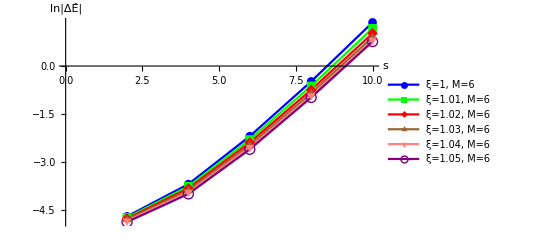
-Graphics-(a) M=6, even s only

```mathematica
Labeled[PlotEvsS[{{1,6},{1.01,6},{1.02,6},{1.03,6},{1.04,6},{1.05,6}},Joined->True, DataSet->2,PlotStyle->{Blue, Green, Red, Brown,Pink,Purple}, AxesOrigin->{0,0},LegendPos->{0.20,0.7}],Style["(a) M=6, even s only",FontSize->LabelFontSize]]
```

M=6, xi=0, slopes={2.03275,2.19694,2.27374,2.32283}, acc={0.164195,0.0767943,0.0490893}, base=-10.2045

M=6, xi=1, slopes={0.164134,0.562955,0.706933,0.770183}, acc={0.398821,0.143978,0.0632505}, base=-2.16016

M=6, xi=2, slopes={2.01455,2.31917,2.49128,2.58981}, acc={0.304612,0.172113,0.0985327}, base=-13.3273

M=6, xi=3, slopes={3.36499,3.58934,3.72472,3.81755}, acc={0.224354,0.135376,0.0928339}, base=-45.4928

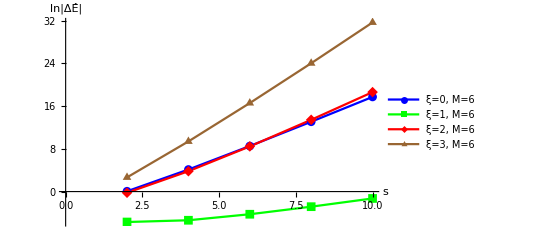
-Graphics-M=6, even s only

M=5, xi=0, slopes={5.47109,-0.0970608,4.0037,0.89842,3.34917,-Log[838284/(125 √5)]+Log[19453/5^(1/4)],2.9365,1.8679,2.63083}, acc={-5.56815,4.10076,-3.10528,2.45075,-1.88185,1.46919,-1.06861,0.762932}, base=-13.8853

M=5, xi=1, slopes={-0.678626,1.26531,-0.971178,2.02061,-0.989128,2.21404,-0.947333,2.28459,-0.910893}, acc={1.94394,-2.23649,2.99178,-3.00973,3.20317,-3.16137,3.23192,-3.19548}, base=-0.402165

M=5, xi=2, slopes={3.02203,2.36241,1.79223,3.33148,1.3951,3.80301,1.23299,4.04638,1.16206}, acc={-0.659624,-0.570172,1.53925,-1.93638,2.4079,-2.57002,2.81339,-2.88432}, base=-3.19651

M=5, xi=3, slopes={4.98268,3.20467,3.58872,4.18881,3.03498,4.72286,2.74769,5.04869,2.58583}, acc={-1.778,0.384045,0.600095,-1.15383,1.68787,-1.97516,2.301,-2.46287}, base=-13.2743

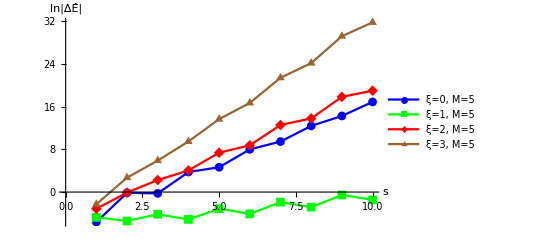
-Graphics-M=5

```mathematica
pevs0=Labeled[PlotEvsS[{{0,6},{1,6},{2,6},{3,6}},Joined->True, DataSet->2,PlotStyle->{Blue, Green, Red, Brown,Pink}, AxesOrigin->{0,0},LegendPos->{0.20,0.7}],Style["M=6, even s only",FontSize->LabelFontSize]]

pevs1=Labeled[PlotEvsS[{{0,5},{1,5},{2,5},{3,5}},Joined->True, DataSet->0,PlotStyle->{Blue, Green, Red, Brown,Pink}, AxesOrigin->{0,0},LegendPos->{0.20,0.7}],Style["M=5",FontSize->LabelFontSize]]

(*Export["EvS-M6.pdf",pevs0];
Export["EvS-M5.pdf",pevs1];*)
ClearAll[pevs0,pevs1]
```

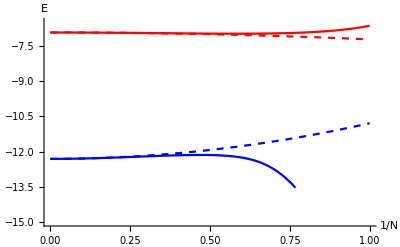
-Graphics-s=1, ξ=0

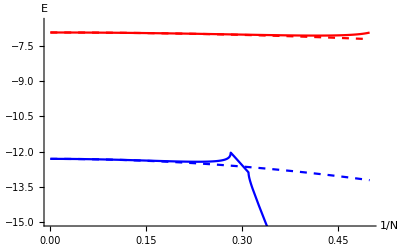
-Graphics-s=1, ξ=1

```mathematica
(* compare the 1/N^2 correction to the exact energy. *)
p1=PlotLowestEnergy[3,0,1,Infinity,Red];
p2=PlotLowestEnergy[5,0,1,Infinity,Blue];
pcompare=Labeled[Show[p1,p2,PlotRange->{{0,1}, {-15,-6.5}},AxesOrigin->Automatic],Style["s=1, ξ=0",FontSize->LabelFontSize]]

p1=PlotLowestEnergy[3,1,2,Infinity,Red];
p2=PlotLowestEnergy[5,1,2,Infinity,Blue];
pcompare2=Labeled[Show[p1,p2,PlotRange->{{0,0.5}, {-15,-6.5}},AxesOrigin->Automatic],Style["s=1, ξ=1",FontSize->LabelFontSize]]

(*Export["EvM-compare.pdf",pcompare];
Export["EvM-compare2.pdf",pcompare2];*)

Clear[p1,p2,pcompare, pcompare2];
```

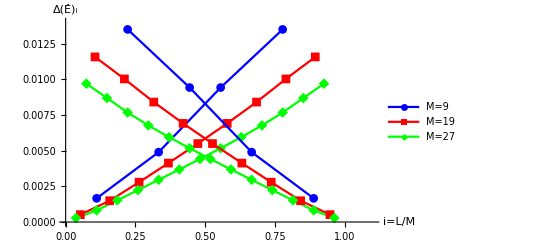
-Graphics-s=1,ξ=0

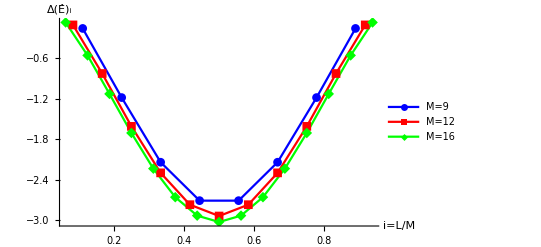
-Graphics-s=2,ξ=0

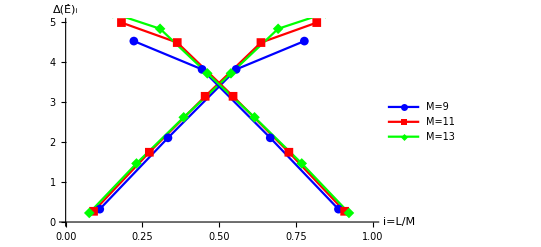
-Graphics-s=3,ξ=0

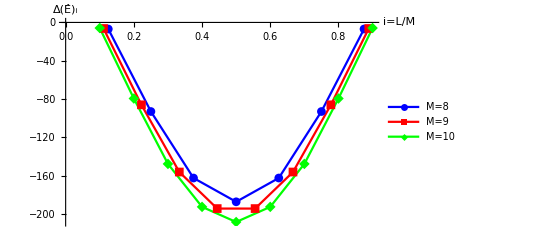
-Graphics-s=4,ξ=0

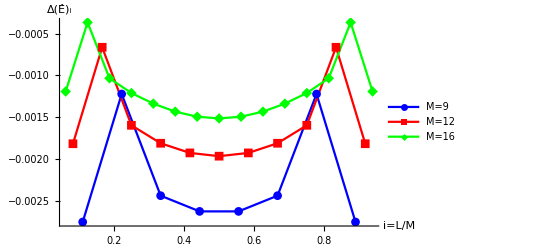
-Graphics-s=2,ξ=1

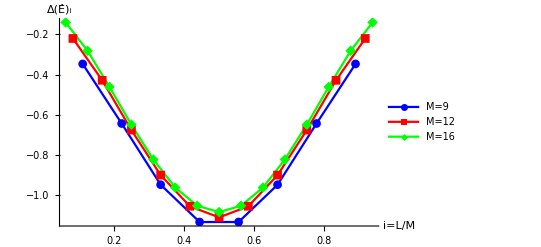
-Graphics-s=2,ξ=2

```mathematica
(* This cell demostrate how Delta Subscript[E, i] changes with respect to i=L/M.*)
p1=PlotEnergyCorrection[1,0,{9,19,27},True, DataSet->1,NormalizeFactorM->2.75,Joined->True,PlotMarkers->Automatic, LegendPos->{0.86,0.39},PlotStyle->{Blue, Red,Green}];
p2=PlotEnergyCorrection[1,0,{9,19,27}, False,DataSet->2,NormalizeFactorM->2.75,Joined->True,PlotMarkers->Automatic,PlotStyle->{Blue, Red,Green}];
ps1=Labeled[Show[p1,p2, PlotRange->{{0,1.1},{0,0.014}}],Style["s=1,ξ=0",FontSize->LabelFontSize]]

ps2=Labeled[PlotEnergyCorrection[2,0,{9,12,16}, True,DataSet->0,NormalizeFactorM->3.5,Joined->True,PlotMarkers->Automatic,LegendPos->{0.14,0.17},PlotRange->{{0,1},{0,-3.5}}, AxesOrigin->{0,0},PlotStyle->{Blue, Red,Green}],Style["s=2,ξ=0",FontSize->LabelFontSize]]

p1=PlotEnergyCorrection[3,0,{9,11,13}, True,DataSet->1,NormalizeFactorM->2.25,Joined->True,PlotMarkers->Automatic,LegendPos->{0.16,0.56},PlotStyle->{Blue, Red,Green}];
p2=PlotEnergyCorrection[3,0,{9,11,13}, False,DataSet->2,NormalizeFactorM->2.25,Joined->True,PlotMarkers->Automatic,PlotStyle->{Blue, Red,Green}(*,LegendPos->{0.18,0.7}*)];
ps3=Labeled[Show[p1,p2, PlotRange->{{0,1},{0,5}}],Style["s=3,ξ=0",FontSize->LabelFontSize]]

ps4=Labeled[PlotEnergyCorrection[4,0,{8,9,10}, True,DataSet->0,NormalizeFactorM->3,Joined->True,PlotMarkers->Automatic,LegendPos->{0.15,0.2},(*PlotRange->{{0,1},{0,-3.5}},*) AxesOrigin->{0,0},PlotStyle->{Blue, Red,Green}],Style["s=4,ξ=0",FontSize->LabelFontSize]]

ps2xi1=Labeled[PlotEnergyCorrection[2,1,{9,12,16}, True,DataSet->0,NormalizeFactorM->3.5,Joined->True,PlotMarkers->Automatic,LegendPos->{0.86,0.3},PlotRange->{{0,1.3},{0,-0.0030}}, AxesOrigin->{0,0},PlotStyle->{Blue, Red,Green}],Style["s=2,ξ=1",FontSize->LabelFontSize]]
ps2xi2=Labeled[PlotEnergyCorrection[2,2,{9,12,16}, True,DataSet->0,NormalizeFactorM->3.5,Joined->True,PlotMarkers->Automatic,LegendPos->{0.15,0.3},PlotRange->{{0,1},{0,-1.5}}, AxesOrigin->{0,0},PlotStyle->{Blue, Red,Green}],Style["s=2,ξ=2",FontSize->LabelFontSize]]

(*Export["SubEvM-s1xi0.pdf",ps1];
Export["SubEvM-s2xi0.pdf",ps2];
Export["SubEvM-s3xi0.pdf",ps3];
Export["SubEvM-s4xi0.pdf",ps4];
Export["SubEvM-s2xi1.pdf",ps2xi1];
Export["SubEvM-s2xi2.pdf",ps2xi2];*)

ClearAll[p1,p2,p11,p12,p21,p22,ps1,ps2,ps3,ps4,ps2xi1,ps2xi2];
```

```mathematica
ClearAll[PlotGammaV];
PlotGammaV[Mlist_,opts:OptionsPattern[]]:=Module[{data={},i,j},
For[j=1,j≤ Length[Mlist],j++,
AppendTo[data, Table[{i/Mlist[[j]],(GammaV2[Mlist[[j]],i,Numeric->True](*+Cot[(2i+1)Pi/(2Mlist[[j]])]*))/Mlist[[j]]},{i,1,Mlist[[j]]-1}]];
];

ListPlot[data,FilterRules[{opts},Options[ListPlot]]]
];

ClearAll[PlotGammaW];
PlotGammaW[Mlist_,opts:OptionsPattern[]]:=Module[{data={},i,j},
For[j=1,j≤ Length[Mlist],j++,
AppendTo[data, Table[{i/Mlist[[j]],(GammaW2[Mlist[[j]],i,Numeric->True](*+Cot[(2i+1)Pi/(2Mlist[[j]])]*))/Mlist[[j]]},{i,1,Mlist[[j]]-1}]];
];

ListPlot[data,FilterRules[{opts},Options[ListPlot]]]
];
```

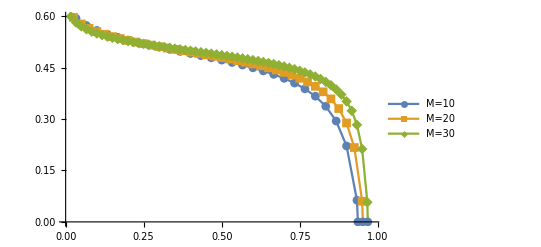

```mathematica
PlotGammaV[{30,40,60},Joined->True, PlotLegends->{"M=10","M=20","M=30","M=40"},PlotMarkers->Automatic]

Clear[tmp1,tmp2,tmp3]
```